```mathematica
Входные данные;
```

```mathematica
ϵ=0.001;α=1;
f[{x_,y_}]:=α(x^2-y)^2+(x-1)^2; X0={-1,-2};
(*f[{x_,y_}]:=10 x^2+7 y^2-4x y-4*5^(1/2)(5x- y)-16; X0={0,-5^(1/2)};*)

uniformMesh[left_,right_,n_]:=Table[i,{i,left,right,(right-left)/n}]
n=2;

Clear[κ,ka, kap];
```

```mathematica
Регулярный симплекс;
```

Результат получен за 290 итер.: X = {0.996875, 0.993426}

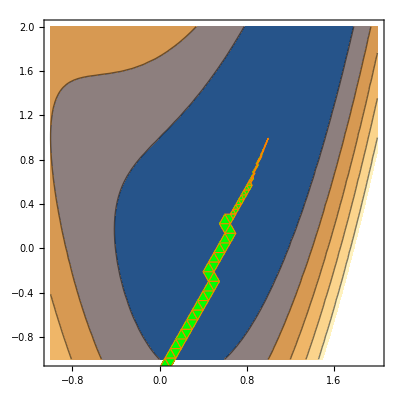

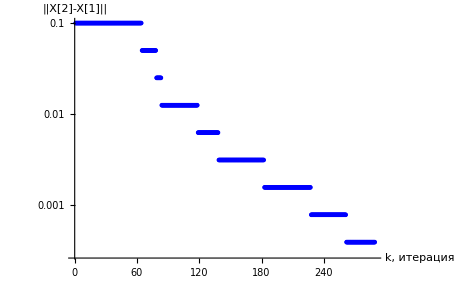

```mathematica
L=0.1; X=Table[0,{j,1,n+1},{i,1,n}];(*вершины симплекса*)
 iterCount=1;simplexes={};
For[i=1,i≤ n+1,i++,
For[j=1,j≤n,j++,
If[j<i-1,X[[i,j]]=X0[[j]],1];
If[j==i-1,X[[i,j]]=X0[[j]]+L √(j/(2(j+1))),1];
If[j>i-1,X[[i,j]]=X0[[j]]-L/(√(2j(j+1))),1];
];
];
count=1;
X=SortBy[X,f[#]&];XC=N[1/n Sum[X[[i]],{i,1,n}]];
dXarray={};
While[ 1/(n+1)Sum[(f[X[[i]]]-f[XC])^2,{i,1,n}]>ϵ^2 ||count<10,
 iterCount++;
X=SortBy[X,f[#]&];
dXarray=Append[dXarray,Norm[X[[2]]-X[[1]]]];
simplexes=Append[simplexes,X];
XC=N[1/n Sum[X[[i]],{i,1,n}]];
Xref=2XC-X[[n+1]];
If[f[Xref]> f[X[[n+1]] ],
count++;
For[i=2,i≤n+1, i++,
δ=0.5;
 X[[i]]= X[[i]]-δ(X[[i]]-X[[1]]);

 ]
, X[[n+1]]=Xref];

];

(*Print[ToString[it]<>": норма градиента = "<>ToString[Round[norm[[-1]],0.01ϵ]]];*)
"Результат получен за "<>ToString[ iterCount]<> " итер.: X = "<>ToString[Xref]
Show[ContourPlot[f[{x,y}],{x,-1,2},{y,-1,2}],{Graphics[{FaceForm[Green],EdgeForm[Directive[Thick,Dashed,Orange]],Polygon[simplexes]}]}]
ListLogPlot[dXarray,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","||X[2]-X[1]||"}]
```

```mathematica
Нерегулярный симплекс;
```

Результат получен за 42 итер.: X = {1.02506, 1.09393}

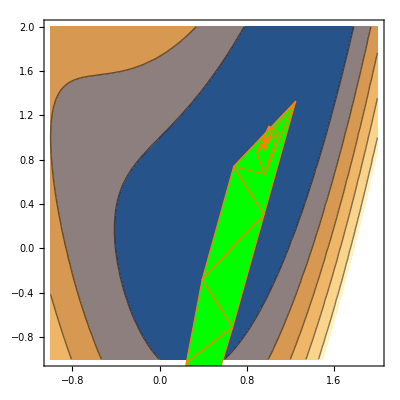

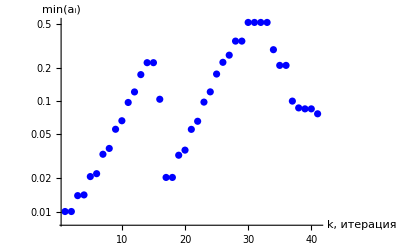

```mathematica
L=0.01; X=Table[0,{j,1,n+1},{i,1,n}];(*вершины симплекса*)
simplexes={};X=Table[0,{j,1,n+1},{i,1,n}];
 iterCount=1;
α=1;
β=1.5;
γ=0.5;
For[i=1,i≤ n+1,i++,
For[j=1,j≤n,j++,
If[j<i-1,X[[i,j]]=X0[[j]],1];
If[j==i-1,X[[i,j]]=X0[[j]]+L √(j/(2(j+1))),1];
If[j>i-1,X[[i,j]]=X0[[j]]-L/(√(2j(j+1))),1];
];
];
X=SortBy[X,f[#]&];
XC=N[1/n Sum[X[[i]],{i,1,n}]];
count=1;
dXarray={};
While[1/(n+1)Sum[(f[X[[i]]]-f[XC])^2,{i,1,n}]>ϵ^2,
iterCount++;
X=SortBy[X,f[#]&];
XC=N[1/n Sum[X[[i]],{i,1,n}]];
dXarray=Append[dXarray,Min[Norm[X[[2]]-X[[1]]],Norm[X[[3]]-X[[1]]],Norm[X[[3]]-X[[2]]]]];
simplexes=Append[simplexes,X];
Xref=XC+α(XC-X[[n+1]]);
If[f[Xref]<f[X[[1]] ],
(*то*)
Xext=XC+β(Xref-XC);
If[f[Xext]<f[Xref ],X[[n+1]]=Xext,X[[n+1]]=Xref],

(*иначе*)
If[f[Xref]>f[X[[n]] ],
(*то*)

XV=If[f[Xref]>f[X[[n+1]]],X[[n+1]],Xref];
Xcom=XC+γ(XV-XC);
If[f[Xcom]<f[X[[n+1]]],X[[n+1]]=Xcom,
(*иначе*)
count++;
For[i=2,i≤n+1, i++,
δ=0.5;
 X[[i]]= X[[i]]+δ(X[[i]]-X[[1]]);

 ];
],
X[[n+1]]=Xref;
];
];

];

(*Print[ToString[it]<>": норма градиента = "<>ToString[Round[norm[[-1]],0.01ϵ]]];*)
"Результат получен за "<>ToString[ iterCount]<> " итер.: X = "<>ToString[Xref]
Show[ContourPlot[f[{x,y}],{x,-1,2},{y,-1,2}],{Graphics[{FaceForm[Green],EdgeForm[Directive[Thick,Dashed,Orange]],Polygon[simplexes]}]}]
ListLogPlot[dXarray,PlotRange->All,Mesh->Full,MeshStyle->PointSize[Large],PlotStyle->{Blue,Thick},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k, итерация","min(a_i)"}]
```